```mathematica
H={{1,1},{1,-1}}/Sqrt[2];
X={{0,1},{1,0}};
Z={{1,0},{0,-1}};
Y={{0,-I},{I,0}};
CNOT={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}; 
NOTC={{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}; 
XNOTC={{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}}; 
%//MatrixForm
Phase[phi_,pauli_]:=MatrixExp[I phi * pauli]
Phase[Pi/8,Z]//MatrixForm
KroneckerProduct[X,H];
%//MatrixForm
%[[{1,2},{2,3}]]//MatrixForm
NToffoli=IdentityMatrix[8];
NToffoli[[{1,2},{1,2}]]=X;
RevNToffoli=IdentityMatrix[8];
RevNToffoli[[{1,5},{1,5}]]=X;
```

(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1)

(ⅇ^((ⅈ π)/8) | 0
0 | ⅇ^(-(ⅈ π)/8))

(0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2)
1/(√2) | 1/(√2) | 0 | 0
1/(√2) | -1/(√2) | 0 | 0)

(0 | 1/(√2)
0 | 1/(√2))

(0.0322461064+0.4121121243 ⅈ | 0.0529849416-0.2854034061 ⅈ | 0.3723431723+0.229761637 ⅈ | 0.4369761703-0.0737237767 ⅈ
-0.4296936598-0.164528617 ⅈ | 0.4089548247+0.362044147 ⅈ | 0.2957024311-0.123791754 ⅈ | 0.139664571-0.2798296139 ⅈ
0.114276695+0.2703145555 ⅈ | -0.1875-0.178909693 ⅈ | -0.196491229+0.2465592057 ⅈ | -0.1740436753+0.0800815355 ⅈ
0.1684698831+0.0539096932 ⅈ | -0.2202465784+0.0417611649 ⅈ | -0.174043675-0.2758883476 ⅈ | 0.0051495125-0.4111873727 ⅈ)

{0.9950777362,0.9366083393,0.3503781081,0.09909742093}

0.+28.0314 x+0. x^2-266.764 x^3+0. x^4+477.465 x^5+0. x^6-238.732 x^7

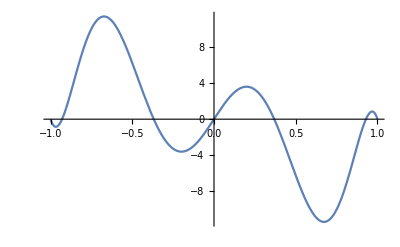

0.+8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

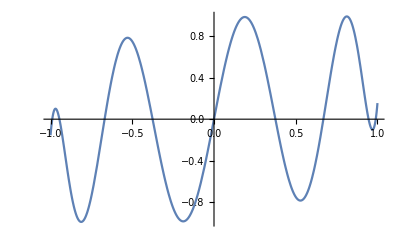

```mathematica
U=KroneckerProduct[NOTC,X].
KroneckerProduct[Phase[Pi/4,Y],Phase[Pi/8,Z],Phase[Pi/16,X]].
KroneckerProduct[Z,NOTC].
KroneckerProduct[Phase[Pi/16,Y],Phase[Pi/8,X],Phase[Pi/4,Y]].
KroneckerProduct[NOTC,Z].KroneckerProduct[Phase[Pi/4,X],Phase[Pi/8,Y],Phase[Pi/16,Z]].KroneckerProduct[X,NOTC].
KroneckerProduct[NOTC,Z].KroneckerProduct[Phase[Pi/16,Y],Phase[Pi/8,X],Phase[Pi/4,Z]];
A=U[[Range[1,4],Range[1,4]]]//N[#,10]&;
A//MatrixForm
SingularValueList[A]
(*Lowest degree problem specific polynomial*)
poly1=InterpolatingPolynomial[{#,1/(4#)}&/@Join[%,-%],x]//Simplify//Chop
Plot[poly1,{x,-1,1}]
(*Optimised problem specific polynomial*)
poly=InterpolatingPolynomial[Join[{#,1/(14#)}&/@Join[%%%,-%%%],{{-0.7,-0.3},{0.7,0.3}}],x];
poly=((poly- (poly/.x->-x))/2)//Simplify
Plot[poly,{x,-1,1}]
```

```mathematica
getPolyPairs[poly_,precision_]:=Module[{polyTry,K,roots,Qp,Zp,SRp,LRp,Ip,Wp,genRoots,zeroRoots,smallRealRoots,largeRealRoots,imgRoots,parityTrick,Bp,Cp},
polyTry=SetPrecision[poly,precision];
degree = (CoefficientList[polyTry,x]//Length)-1;
(K=Sqrt[-Coefficient[(1-polyTry^2//Expand),x^(2 degree)]])//Precision;
roots=x/.NSolve[(1-polyTry^2//Expand)==0,x,WorkingPrecision->precision];
(*p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]*)
(genRoots=Select[roots,(Re[#]>0&& Im[#]>0)&]);
zeroRoots=(Select[roots,(#==0)&]);
smallRealRoots=(Select[roots,(#!=0&&Re[#]>-1&&Re[#]<1&& Im[#]==0)&]);
(smallRealRoots=Table[smallRealRoots[[4i-3]],{i,1,(smallRealRoots//Length)/4}]);
(largeRealRoots=Select[roots,(Re[#]≥1&& Im[#]==0)&]);
(imgRoots=Select[roots,(Re[#]==0&& Im[#]>0)&]);
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@genRoots) ;
Zp=x^((zeroRoots//Length)/2);
SRp=(x^2-#^2)&/@smallRealRoots;
LRp=(Sqrt[#^2-1]x+I # Sqrt[1-x^2])&/@largeRealRoots;
Ip=(Sqrt[Abs[#]^2+1]x-I Abs[#]Sqrt[1-x^2])&/@imgRoots;
Wp=K*(Times@@Qp)*Zp*(Times@@SRp)*(Times@@LRp)*(Times@@Ip)//Expand//Simplify;
parityTrick=SetPrecision[Wp/.{Sqrt[1-x^2]->-I},precision];
Bp=SetPrecision[(parityTrick+(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
Cp=SetPrecision[(parityTrick-(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
{Bp,Cp}
]
{Bp,Cp}=getPolyPairs[ChebyshevT[5,x] ,110];
Bp^2+(1-x^2)Cp^2+ChebyshevT[5,x]^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
{Bp,Cp}=getPolyPairs[poly,30];
poly=SetPrecision[poly,30];
Bp^2+(1-x^2)Cp^2+poly^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
```

True

True

```mathematica
carveLastAngle[Mat_]:=Module[{angle,outMat},
angle=(Coefficient[Mat[[1,1]],x,Exponent[Mat[[1,1]],x]]/(Coefficient[Mat[[1,2]]/.{Sqrt[1-x^2]->-I},x,(Exponent[Mat[[1,1]],x]-1)]))//Sqrt;
outMat=Mat.{{Conjugate[angle],0},{0,angle}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand;
outMat=outMat/.x^b_/;b≥Exponent[Mat[[1,1]],x]+1->0;
outMat=outMat/.Sqrt[1-x^2]x^b_/;b≥Exponent[Mat[[1,1]],x]->0;
{outMat, angle}
];
getMatrix[phs_]:=Module[{phaseGates,W},
phaseGates=Table[{{phs[[i]],0},{0,Conjugate[phs[[i]]]}},{i,1,Length[phs]}];
(W={{x,I Sqrt[1-x^2]},{I Sqrt[1-x^2],x}})//MatrixForm;
(Dot@@((phaseGates//Most).W)).(phaseGates//Last)//Expand
];
getPhases[poly_,precision_]:=Module[{tmpPoly,agreement,tmpprecision,Bp,Cp,Mat,carved,phs,phaseGates,W,NewMat},
agreement=1;
tmpprecision=MachinePrecision;
phs={};
While[ ((agreement//Accuracy) <precision) ||(agreement>10^-precision),
tmpPoly=SetPrecision[poly,tmpprecision];
{Bp,Cp}=getPolyPairs[tmpPoly,tmpprecision];
(Mat={{tmpPoly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,tmpPoly-I Bp}})//MatrixForm;
carved=NestList[carveLastAngle[#[[1]]]&,{Mat,{}},(tmpPoly//CoefficientList[#,x]&//Length)-1];
phs=Join[{(carved//Last)[[1]][[1]][[1]]},(#[[2]]&/@ carved)//Reverse//Most];
NewMat=getMatrix[phs];
agreement=(NewMat[[1,1]]-tmpPoly-I Bp)//Expand//CoefficientList[#,x]&//Abs//Total;
Print[tmpprecision];
tmpprecision=2tmpprecision];
phs
];
phs=getPhases[ChebyshevT[10,x],20];
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

```mathematica
(Mat={{poly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,poly-I Bp}})
ph9=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop
ph8=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph7=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph6=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph5=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph4=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph3=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph2=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph1=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(%[[1,2]]/.{Sqrt[1-x^2]->-I})//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph0=%[[1,1]]
(R={{x,Sqrt[1-x^2]},{Sqrt[1-x^2],-x}})//MatrixForm
phs={I*ph0*ph9,ph1,ph2,ph3,ph4,ph5,ph6,ph7,ph8}/I//Arg;
NewMat=Dot@@Table[Phase[phs[[i]],Z].R,{i,1,Length[phs]}]//Expand//Simplify;
NewMat[[1,1]]-poly-I Bp//Expand//CoefficientList[#,x]&//Norm[#,1]&
```

{{8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9+ⅈ (2.65345600801895827896067580403 x-53.9368676154080219198244623338 x^3+223.970773786938501425467463889 x^5-326.26737682709360445285551463 x^7+154.568016291768987976733667945 x^9),√(1-x^2) (1.-36.3409764740634686417109235802 x^2+210.010511043757036363608365414 x^4-379.942412673639640437807501274 x^6+213.640738463311759396046573291 x^8)},{-√(1-x^2) (1.-36.3409764740634686417109235802 x^2+210.010511043757036363608365414 x^4-379.942412673639640437807501274 x^6+213.640738463311759396046573291 x^8),8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9-ⅈ (2.65345600801895827896067580403 x-53.9368676154080219198244623338 x^3+223.970773786938501425467463889 x^5-326.26737682709360445285551463 x^7+154.568016291768987976733667945 x^9)}}

0.37182317852409984934638156127+0.928303573144171072558151416234 ⅈ

{{(0.92830357314417107255815141623-0.37182317852409984934638156127 ⅈ)-(29.165207296304529950861825816-7.292742220959100677681180127 ⅈ) x^2+(143.84061128652233340469992743-24.82507903147073768231218605 ⅈ) x^4-(227.74268665862686139521798789-23.01390904261842237272501434 ⅈ) x^6+(113.1135701723597508819542665-4.88575746345691131106324915 ⅈ) x^8,(-6.2196751622967131015401793362-4.5702510161168473740881593332 ⅈ) x √(1-x^2)+(53.261696708289577837455903775+51.112896513230723421192600355 ⅈ) x^3 √(1-x^2)-(118.2574864938095068041931501+124.9592126153300048831244087 ⅈ) x^5 √(1-x^2)+(74.55082097420758231521754605+85.20989071229189918468325932 ⅈ) x^7 √(1-x^2)},{(6.2196751622967131015401793362-4.5702510161168473740881593332 ⅈ) x √(1-x^2)-(53.261696708289577837455903775-51.112896513230723421192600355 ⅈ) x^3 √(1-x^2)+(118.2574864938095068041931501-124.9592126153300048831244087 ⅈ) x^5 √(1-x^2)-(74.55082097420758231521754605-85.20989071229189918468325932 ⅈ) x^7 √(1-x^2),(0.92830357314417107255815141623+0.37182317852409984934638156127 ⅈ)-(29.165207296304529950861825816+7.292742220959100677681180127 ⅈ) x^2+(143.84061128652233340469992743+24.82507903147073768231218605 ⅈ) x^4-(227.74268665862686139521798789+23.01390904261842237272501434 ⅈ) x^6+(113.1135701723597508819542665+4.88575746345691131106324915 ⅈ) x^8}}

0.9434841690858956105218426269+0.331417595616613484544345119 ⅈ

0.99358319114199946846053338+0.1131036793392723762685438 ⅈ

0.9976734097614405695544326+0.0681745367052882939036933 ⅈ

0.976775599092318899444285-0.2142648571694422836577 ⅈ

0.9767755990923188994443-0.2142648571694422836577 ⅈ

0.997673409761440569554+0.068174536705288293904 ⅈ

0.99358319114199946846+0.1131036793392723763 ⅈ

0.9434841690858956105+0.3314175956166134845 ⅈ

0.9283035731441710726-0.3718231785240998493 ⅈ

(x | √(1-x^2)
√(1-x^2) | -x)

0

```mathematica
HHL=Dot@@Table[KroneckerProduct[XNOTC,IdentityMatrix[4]].KroneckerProduct[Phase[phs[[i]],Z],IdentityMatrix[8]].KroneckerProduct[XNOTC,IdentityMatrix[4]].KroneckerProduct[IdentityMatrix[2],MatrixPower[U//N,(-1)^i]],{i,1,Length[phs]}];
HHL=KroneckerProduct[H,IdentityMatrix[8]].HHL.KroneckerProduct[H,IdentityMatrix[8]];
HHL[[1;;4,1;;4]];
%//MatrixForm
(%%*14-AInv)//Norm
```

(0.123302+0.0612786 ⅈ | -0.152829-0.0961579 ⅈ | -0.285155-0.164685 ⅈ | 0.126288-0.179026 ⅈ
0.145875+0.0869695 ⅈ | -0.105248-0.107894 ⅈ | -0.321182-0.0670514 ⅈ | 0.0644302-0.211255 ⅈ
-0.0438065-0.122915 ⅈ | 0.101795+0.0066714 ⅈ | 0.141445-0.026424 ⅈ | -0.14997+0.0860774 ⅈ
0.092266+0.107257 ⅈ | -0.0831759+0.0223294 ⅈ | -0.18533-0.00368527 ⅈ | 0.126955-0.0112672 ⅈ)

Max[√Root[(954.93-5.45697×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(3.43903×10^-12+1.36424×10^-12 ⅈ) AInv^2-(1.25527×10^-13-6.67299×10^-14 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.09228×10^-11 ⅈ) AInv Conjugate[AInv]+(2.72848×10^-12-3.63798×10^-12 ⅈ) AInv^2 Conjugate[AInv]-(7.69027×10^-13+3.48875×10^-13 ⅈ) AInv^3 Conjugate[AInv]-(3.58114×10^-12+1.40687×10^-12 ⅈ) Conjugate[AInv]^2+(2.16005×10^-12-1.36424×10^-11 ⅈ) AInv Conjugate[AInv]^2+(1.81899×10^-12+6.82121×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(4.54747×10^-13-4.54747×10^-13 ⅈ) AInv^3 Conjugate[AInv]^2+(6.62409×10^-13-2.08265×10^-13 ⅈ) Conjugate[AInv]^3+(4.39097×10^-13+1.07136×10^-12 ⅈ) AInv Conjugate[AInv]^3-(8.47334×10^-13+7.52644×10^-15 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+3.18323×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(6.11067×10^-13-2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03-1.36424×10^-12 ⅈ) AInv Conjugate[AInv]-4.54747×10^-13 AInv^2 Conjugate[AInv]-(0.+1.7053×10^-13 ⅈ) Conjugate[AInv]^2-(1.13687×10^-13-2.27374×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(5.18762×10^-14-3.54874×10^-14 ⅈ) AInv Conjugate[AInv]^3+(1.42109×10^-14-2.13163×10^-14 ⅈ) AInv^2 Conjugate[AInv]^3) #1+((1067.05+6.21725×10^-14 ⅈ)+(116.609-308.161 ⅈ) AInv+(0.+1.77636×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-2.84217×10^-14 ⅈ) AInv Conjugate[AInv]+(1.06581×10^-14-1.06581×10^-14 ⅈ) Conjugate[AInv]^2-(0.+1.42109×10^-14 ⅈ) AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,1],√Root[(954.93-5.45697×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(3.43903×10^-12+1.36424×10^-12 ⅈ) AInv^2-(1.25527×10^-13-6.67299×10^-14 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.09228×10^-11 ⅈ) AInv Conjugate[AInv]+(2.72848×10^-12-3.63798×10^-12 ⅈ) AInv^2 Conjugate[AInv]-(7.69027×10^-13+3.48875×10^-13 ⅈ) AInv^3 Conjugate[AInv]-(3.58114×10^-12+1.40687×10^-12 ⅈ) Conjugate[AInv]^2+(2.16005×10^-12-1.36424×10^-11 ⅈ) AInv Conjugate[AInv]^2+(1.81899×10^-12+6.82121×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(4.54747×10^-13-4.54747×10^-13 ⅈ) AInv^3 Conjugate[AInv]^2+(6.62409×10^-13-2.08265×10^-13 ⅈ) Conjugate[AInv]^3+(4.39097×10^-13+1.07136×10^-12 ⅈ) AInv Conjugate[AInv]^3-(8.47334×10^-13+7.52644×10^-15 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+3.18323×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(6.11067×10^-13-2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03-1.36424×10^-12 ⅈ) AInv Conjugate[AInv]-4.54747×10^-13 AInv^2 Conjugate[AInv]-(0.+1.7053×10^-13 ⅈ) Conjugate[AInv]^2-(1.13687×10^-13-2.27374×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(5.18762×10^-14-3.54874×10^-14 ⅈ) AInv Conjugate[AInv]^3+(1.42109×10^-14-2.13163×10^-14 ⅈ) AInv^2 Conjugate[AInv]^3) #1+((1067.05+6.21725×10^-14 ⅈ)+(116.609-308.161 ⅈ) AInv+(0.+1.77636×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-2.84217×10^-14 ⅈ) AInv Conjugate[AInv]+(1.06581×10^-14-1.06581×10^-14 ⅈ) Conjugate[AInv]^2-(0.+1.42109×10^-14 ⅈ) AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,2],√Root[(954.93-5.45697×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(3.43903×10^-12+1.36424×10^-12 ⅈ) AInv^2-(1.25527×10^-13-6.67299×10^-14 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.09228×10^-11 ⅈ) AInv Conjugate[AInv]+(2.72848×10^-12-3.63798×10^-12 ⅈ) AInv^2 Conjugate[AInv]-(7.69027×10^-13+3.48875×10^-13 ⅈ) AInv^3 Conjugate[AInv]-(3.58114×10^-12+1.40687×10^-12 ⅈ) Conjugate[AInv]^2+(2.16005×10^-12-1.36424×10^-11 ⅈ) AInv Conjugate[AInv]^2+(1.81899×10^-12+6.82121×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(4.54747×10^-13-4.54747×10^-13 ⅈ) AInv^3 Conjugate[AInv]^2+(6.62409×10^-13-2.08265×10^-13 ⅈ) Conjugate[AInv]^3+(4.39097×10^-13+1.07136×10^-12 ⅈ) AInv Conjugate[AInv]^3-(8.47334×10^-13+7.52644×10^-15 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+3.18323×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(6.11067×10^-13-2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03-1.36424×10^-12 ⅈ) AInv Conjugate[AInv]-4.54747×10^-13 AInv^2 Conjugate[AInv]-(0.+1.7053×10^-13 ⅈ) Conjugate[AInv]^2-(1.13687×10^-13-2.27374×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(5.18762×10^-14-3.54874×10^-14 ⅈ) AInv Conjugate[AInv]^3+(1.42109×10^-14-2.13163×10^-14 ⅈ) AInv^2 Conjugate[AInv]^3) #1+((1067.05+6.21725×10^-14 ⅈ)+(116.609-308.161 ⅈ) AInv+(0.+1.77636×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-2.84217×10^-14 ⅈ) AInv Conjugate[AInv]+(1.06581×10^-14-1.06581×10^-14 ⅈ) Conjugate[AInv]^2-(0.+1.42109×10^-14 ⅈ) AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,3],√Root[(954.93-5.45697×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(3.43903×10^-12+1.36424×10^-12 ⅈ) AInv^2-(1.25527×10^-13-6.67299×10^-14 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.09228×10^-11 ⅈ) AInv Conjugate[AInv]+(2.72848×10^-12-3.63798×10^-12 ⅈ) AInv^2 Conjugate[AInv]-(7.69027×10^-13+3.48875×10^-13 ⅈ) AInv^3 Conjugate[AInv]-(3.58114×10^-12+1.40687×10^-12 ⅈ) Conjugate[AInv]^2+(2.16005×10^-12-1.36424×10^-11 ⅈ) AInv Conjugate[AInv]^2+(1.81899×10^-12+6.82121×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(4.54747×10^-13-4.54747×10^-13 ⅈ) AInv^3 Conjugate[AInv]^2+(6.62409×10^-13-2.08265×10^-13 ⅈ) Conjugate[AInv]^3+(4.39097×10^-13+1.07136×10^-12 ⅈ) AInv Conjugate[AInv]^3-(8.47334×10^-13+7.52644×10^-15 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+3.18323×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(6.11067×10^-13-2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03-1.36424×10^-12 ⅈ) AInv Conjugate[AInv]-4.54747×10^-13 AInv^2 Conjugate[AInv]-(0.+1.7053×10^-13 ⅈ) Conjugate[AInv]^2-(1.13687×10^-13-2.27374×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(5.18762×10^-14-3.54874×10^-14 ⅈ) AInv Conjugate[AInv]^3+(1.42109×10^-14-2.13163×10^-14 ⅈ) AInv^2 Conjugate[AInv]^3) #1+((1067.05+6.21725×10^-14 ⅈ)+(116.609-308.161 ⅈ) AInv+(0.+1.77636×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-2.84217×10^-14 ⅈ) AInv Conjugate[AInv]+(1.06581×10^-14-1.06581×10^-14 ⅈ) Conjugate[AInv]^2-(0.+1.42109×10^-14 ⅈ) AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,4]]

```mathematica
AInv=Inverse[A]
NA=Table[(Abs[#^2]&)/@(AInv.IdentityMatrix[4][[k]]//Normalize),{k,1,4}]//Transpose;
NA//MatrixForm
BarChart3D[(*Reverse/@*)NA//Transpose,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"Canvas"->False,"FaceGrids"->None][[1]]//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

{{1.726228946+0.8578997963 ⅈ,-2.13961007-1.346210407 ⅈ,-3.992171309-2.305589806 ⅈ,1.768034838-2.506358879 ⅈ},{2.042253794+1.217573507 ⅈ,-1.473471054-1.510519578 ⅈ,-4.496544141-0.9387190898 ⅈ,0.902023419-2.957568113 ⅈ},{-0.6132908995-1.7208139 ⅈ,1.425133879+0.09339966273 ⅈ,1.980230671-0.3699363492 ⅈ,-2.099578091+1.205083362 ⅈ},{1.291723408+1.50160151 ⅈ,-1.164462761+0.312612052 ⅈ,-2.594616637-0.05159377029 ⅈ,1.777369124-0.1577405162 ⅈ}}

(0.223445407 | 0.445732567 | 0.399900633 | 0.335836116
0.339948566 | 0.310592411 | 0.397020398 | 0.341300483
0.20068316 | 0.142276011 | 0.0763586256 | 0.209204692
0.235922868 | 0.101399011 | 0.126720343 | 0.113658709)

-Graphics3D-

```mathematica
AInv//Round[#,0.1]&//MatrixForm
BarChart3D[(*Reverse/@*)AInv//Transpose//Abs//#^1&,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"Canvas"->False,"FaceGrids"->None][[1]]//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

(1.7+0.9 ⅈ | -2.1-1.3 ⅈ | -4.-2.3 ⅈ | 1.8-2.5 ⅈ
2.+1.2 ⅈ | -1.5-1.5 ⅈ | -4.5-0.9 ⅈ | 0.9-3. ⅈ
-0.6-1.7 ⅈ | 1.4+0.1 ⅈ | 2.-0.4 ⅈ | -2.1+1.2 ⅈ
1.3+1.5 ⅈ | -1.2+0.3 ⅈ | -2.6-0.1 ⅈ | 1.8-0.2 ⅈ)

-Graphics3D-

8.16340150682514398283728951355 x-93.535233688532741780363721773 x^3+301.218044752806861197313992307 x^5-363.174288416582953686884138733 x^7+147.48251920406232784444000572 x^9

0.986250969199471464906607

{0.9950777362,0.9366083393,0.3503781081,0.09909742093}

0.+112.125 x-1067.05 x^3+1909.86 x^5-954.93 x^7

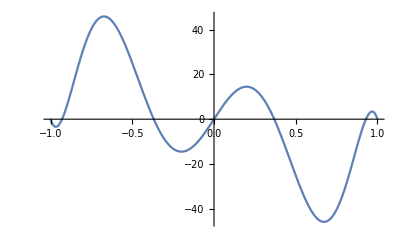

45.835

0.+112.125 x-1067.05 x^3+1909.86 x^5-954.93 x^7

-Graphics-

45.835

```mathematica
(*Finds the largest absolute value on the interval [-1,1]*)
findPolyMaxAbs[poly_]:=Module[{roots,optimaCandidates},
roots=x/.NSolve[(D[poly,x]//Evaluate)==0,x];
optimaCandidates=Join[{-1},roots,{1}];
(poly/.x->optimaCandidates)//Abs//Max
]
(*Lowest degree problem specific polynomial*)
fitOddPoly[singularValues_]:=fitOptimizedPoly[singularValues,0,1]
(*Optimise the magnitude of the polynomial on [-1,1]*)
fitOptimizedPoly[singularValues_,numExtraPoints_,numRandomTrials_]:=Module[{fitPoints,tmpPoly,currentMinMax,currentBestPoly},
currentMinMax=Infinity;
For[j=0,j<numRandomTrials,j++,
fitPoints=Join[singularValues,Table[RandomReal[{0,2}],{k,1,numExtraPoints}]];
fitPoints=DeleteCases[Join[fitPoints,-fitPoints]//N,0.0];
tmpPoly=InterpolatingPolynomial[{#,1/#}&/@fitPoints,x];
tmpPoly=((tmpPoly- (tmpPoly/.x->-x))/2)//Simplify;
currentBestPoly=If[findPolyMaxAbs[tmpPoly]<currentMinMax,tmpPoly,currentBestPoly];
currentMinMax=If[findPolyMaxAbs[tmpPoly]<currentMinMax,findPolyMaxAbs[tmpPoly],currentMinMax];
];
currentBestPoly
]
poly=8.1634015068251439828372895135544240474700927734375`30. x-93.53523368853274178036372177302837371826171875`30. x^3+301.21804475280686119731399230659008026123046875`30. x^5-363.1742884165829536868841387331485748291015625`30. x^7+147.482519204062327844440005719661712646484375`30. x^9
findPolyMaxAbs[%]
SingularValueList[A]
%//fitOddPoly
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
fitOptimizedPoly[%%%%,0,100]
Plot[%,{x,-1,1}]
%%//findPolyMaxAbs
```